```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Critical-region/QCD

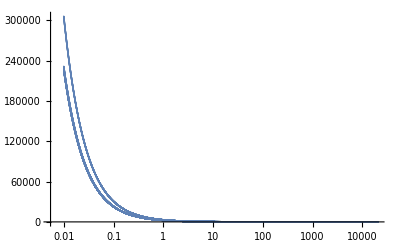

```mathematica
k=Flatten[Import["./v1/BUFFER/K.DAT"]];
rho=Flatten[Import["./v1/BUFFER/RHO.DAT"]];
ListPlot[Transpose[{k,rho[[1;;Length[k]]]/k}],ScalingFunctions->{"Log",Automatic},PlotRange->{All,All}]
```

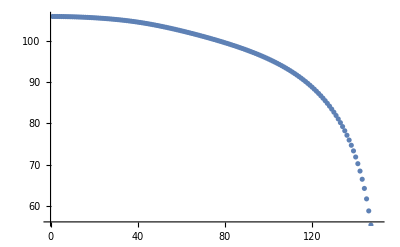

```mathematica
sigma=Flatten[Import["./v1/BUFFER/FPI.DAT"]];
ListPlot[sigma]
```